```mathematica
(*用于将各图变为对应的实际中间粒子*)
```

```mathematica
(*先以图b为例吧*)
```

```mathematica
(*把中间粒子的输入关系和具体衰变道的系数分开输入*)
```

```mathematica
(*图b计算结果*)
```

```mathematica
Dc=0.76;
Fc=0.5;
fc=0.093;
```

```mathematica
dgpdu=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-b-dleta-up-xi1.wdx"];
dHdgu=Query[1,1]@dgpdu;
dHeru=Query[1,2]@dgpdu;
dHdau=Query[1,3]@dgpdu;
dEdgu=Query[2,1]@dgpdu;
dEeru=Query[2,2]@dgpdu;
dEdau=Query[2,3]@dgpdu;
dHdgfu=Interpolation[Flatten[dHdgu,1]];
dHerfu=Interpolation[Flatten[dHeru,1]];

dEdgfu=Interpolation[Flatten[dEdgu,1]];
dEerfu=Interpolation[Flatten[dEeru,1]];
```

```mathematica
dgpdd=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-b-dleta-dp-xi1.wdx"];
dHdgd=Query[1,1]@dgpdd;
dHerd=Query[1,2]@dgpdd;
dHdad=Query[1,3]@dgpdd;
dEdgd=Query[2,1]@dgpdd;
dEerd=Query[2,2]@dgpdd;
dEdad=Query[2,3]@dgpdd;
dHdgfd=Interpolation[Flatten[dHdgd,1]];
dHerfd=Interpolation[Flatten[dHerd,1]];

dEdgfd=Interpolation[Flatten[dEdgd,1]];
dEerfd=Interpolation[Flatten[dEerd,1]];
```

```mathematica
gpdu=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-b-up-xi1.wdx"];
Hdgu=Query[1,1]@gpdu;
Heru=Query[1,2]@gpdu;
Hdau=Query[1,3]@gpdu;
Edgu=Query[2,1]@gpdu;
Eeru=Query[2,2]@gpdu;
Edau=Query[2,3]@gpdu;
Hdgfu=Interpolation[Flatten[Hdgu,1]];
Herfu=Interpolation[Flatten[Heru,1]];
Hdafu=Interpolation[Flatten[Hdau,1]];
Edgfu=Interpolation[Flatten[Edgu,1]];
Eerfu=Interpolation[Flatten[Eeru,1]];
Edafu=Interpolation[Flatten[Edau,1]];
```

```mathematica
gpdd=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-b-dp-xi1.wdx"];
Hdgd=Query[1,1]@gpdd;
Herd=Query[1,2]@gpdd;
Hdad=Query[1,3]@gpdd;
Edgd=Query[2,1]@gpdd;
Eerd=Query[2,2]@gpdd;
Edad=Query[2,3]@gpdd;
Hdgfd=Interpolation[Flatten[Hdgd,1]];
Herfd=Interpolation[Flatten[Herd,1]];
Hdafd=Interpolation[Flatten[Hdad,1]];
Edgfd=Interpolation[Flatten[Edgd,1]];
Eerfd=Interpolation[Flatten[Eerd,1]];
Edafd=Interpolation[Flatten[Edad,1]];
```

```mathematica
Hdgf1u[x_,t_]:=Chop[Hdgfu[x,t],10^-7];
Herf1u[x_,t_]:=Chop[Herfu[x,t],10^-7]+Chop[Hdafu[x,t],10^-7];
Edgf1u[x_,t_]:=Chop[Edgfu[x,t],10^-7];
Eerf1u[x_,t_]:=Chop[Eerfu[x,t],10^-7]+Chop[Edafu[x,t],10^-7];
```

```mathematica
Hdgf1d[x_,t_]:=Chop[Hdgfd[x,t],10^-7];
Herf1d[x_,t_]:=Chop[Herfd[x,t],10^-7]+Chop[Hdafd[x,t],10^-7];
Edgf1d[x_,t_]:=Chop[Edgfd[x,t],10^-7];
Eerf1d[x_,t_]:=Chop[Eerfd[x,t],10^-7]+Chop[Edafd[x,t],10^-7];
```

```mathematica
(*original result fron the calculation*)
```

```mathematica
Hdgfnu[x_,t_]:=Hdgf1u[x,t]+dHdgfu[x,t];
Herfnu[x_,t_]:=Herf1u[x,t]+dHerfu[x,t];
Edgfnu[x_,t_]:=Edgf1u[x,t]+dEdgfu[x,t];
Eerfnu[x_,t_]:=Eerf1u[x,t]+dEerfu[x,t];
```

```mathematica
Hdgfnd[x_,t_]:=Hdgf1d[x,t]+dHdgfd[x,t];
Herfnd[x_,t_]:=Herf1d[x,t]+dHerfd[x,t];
Edgfnd[x_,t_]:=Edgf1d[x,t]+dEdgfd[x,t];
Eerfnd[x_,t_]:=Eerf1d[x,t]+dEerfd[x,t];
```

```mathematica
(*result of p pi0 as input*)
```

```mathematica
pCoe=(1/(2*(2π)^4))*(-I)*((Dc+Fc)^2/(4fc^2));
```

```mathematica
pHdgu[x_,t_]:=pCoe*Hdgfnu[x,t];
pHeru[x_,t_]:=pCoe*Herfnu[x,t];
pEdgu[x_,t_]:=pCoe*Edgfnu[x,t];
pEeru[x_,t_]:=pCoe*Eerfnu[x,t];

pHdgd[x_,t_]:=pCoe*Hdgfnd[x,t];
pHerd[x_,t_]:=pCoe*Herfnd[x,t];
pEdgd[x_,t_]:=pCoe*Edgfnd[x,t];
pEerd[x_,t_]:=pCoe*Eerfnd[x,t];
```

```mathematica
(*result of p η8 as input,不过应该不考虑这个*)
```

```mathematica
p2Coe=(1/(2*(2π)^4))*(-I)*((Dc-3Fc)^2/(12fc^2));
```

```mathematica
pHdgu2[x_,t_]:=p2Coe*Hdgfnu[x,t];
pHeru2[x_,t_]:=p2Coe*Herfnu[x,t];
pEdgu2[x_,t_]:=p2Coe*Edgfnu[x,t];
pEeru2[x_,t_]:=p2Coe*Eerfnu[x,t];

pHdgd2[x_,t_]:=p2Coe*Hdgfnd[x,t];
pHerd2[x_,t_]:=p2Coe*Herfnd[x,t];
pEdgd2[x_,t_]:=p2Coe*Edgfnd[x,t];
pEerd2[x_,t_]:=p2Coe*Eerfnd[x,t];
```

```mathematica
(*npi+*)
```

```mathematica
nCoe=(1/(2*(2π)^4))*(-I)*((Dc+Fc)^2/(2fc^2));
```

```mathematica
nHdgu[x_,t_]:=nCoe*Hdgfnd[x,t];
nHeru[x_,t_]:=nCoe*Herfnd[x,t];
nEdgu[x_,t_]:=nCoe*Edgfnd[x,t];
nEeru[x_,t_]:=nCoe*Eerfnd[x,t];

nHdgd[x_,t_]:=nCoe*Hdgfnu[x,t];
nHerd[x_,t_]:=nCoe*Herfnu[x,t];
nEdgd[x_,t_]:=nCoe*Edgfnu[x,t];
nEerd[x_,t_]:=nCoe*Eerfnu[x,t];
```

```mathematica
(*k0-Σ+*)
```

```mathematica
S1Coe=(1/(2*(2π)^4))*(-I)*((Dc-Fc)^2/(2fc^2));
```

```mathematica
s1Hdgu[x_,t_]:=S1Coe*Hdgfnu[x,t];
s1Heru[x_,t_]:=S1Coe*Herfnu[x,t];
s1Edgu[x_,t_]:=S1Coe*Edgfnu[x,t];
s1Eeru[x_,t_]:=S1Coe*Eerfnu[x,t];

s1Hdgs[x_,t_]:=S1Coe*Hdgfnd[x,t];
s1Hers[x_,t_]:=S1Coe*Herfnd[x,t];
s1Edgs[x_,t_]:=S1Coe*Edgfnd[x,t];
s1Eers[x_,t_]:=S1Coe*Eerfnd[x,t];
```

```mathematica
(*k+-Σ0*)
```

```mathematica
S0Coe=(1/(2*(2π)^4))*(-I)*((Dc-Fc)^2/(4fc^2));
```

```mathematica
s0Hdgu[x_,t_]:=S0Coe*(1/2)Hdgfnu[x,t];
s0Heru[x_,t_]:=S0Coe*(1/2)Herfnu[x,t];
s0Edgu[x_,t_]:=S0Coe*(1/2)Edgfnu[x,t];
s0Eeru[x_,t_]:=S0Coe*(1/2)Eerfnu[x,t];

s0Hdgd[x_,t_]:=S0Coe*(1/2)Hdgfnu[x,t];
s0Herd[x_,t_]:=S0Coe*(1/2)Herfnu[x,t];
s0Edgd[x_,t_]:=S0Coe*(1/2)Edgfnu[x,t];
s0Eerd[x_,t_]:=S0Coe*(1/2)Eerfnu[x,t];

s0Hdgs[x_,t_]:=S0Coe*Hdgfnd[x,t];
s0Hers[x_,t_]:=S0Coe*Herfnd[x,t];
s0Edgs[x_,t_]:=S0Coe*Edgfnd[x,t];
s0Eers[x_,t_]:=S0Coe*Eerfnd[x,t];
```

```mathematica
(*k+-Λ*)
```

```mathematica
LCoe=(1/(2*(2π)^4))*(-I)*((Dc+3Fc)^2/(12fc^2));
```

```mathematica
lHdgu[x_,t_]:=LCoe*(1/6)(Hdgfnu[x,t]+4Hdgfnd[x,t]);
lHeru[x_,t_]:=LCoe*(1/6)(Herfnu[x,t]+4Herfnd[x,t]);
lEdgu[x_,t_]:=LCoe*(1/6)(Edgfnu[x,t]+4Edgfnd[x,t]);
lEeru[x_,t_]:=LCoe*(1/6)(Eerfnu[x,t]+4Eerfnd[x,t]);

lHdgd[x_,t_]:=LCoe*(1/6)(Hdgfnu[x,t]+4Hdgfnd[x,t]);
lHerd[x_,t_]:=LCoe*(1/6)(Herfnu[x,t]+4Herfnd[x,t]);
lEdgd[x_,t_]:=LCoe*(1/6)(Edgfnu[x,t]+4Edgfnd[x,t]);
lEerd[x_,t_]:=LCoe*(1/6)(Eerfnu[x,t]+4Eerfnd[x,t]);

lHdgs[x_,t_]:=LCoe*(1/3)(2Hdgfnu[x,t]-Hdgfnd[x,t]);
lHers[x_,t_]:=LCoe*(1/3)(2Herfnu[x,t]-Herfnd[x,t]);
lEdgs[x_,t_]:=LCoe*(1/3)(2Edgfnu[x,t]-Edgfnd[x,t]);
lEers[x_,t_]:=LCoe*(1/3)(2Eerfnu[x,t]-Eerfnd[x,t]);
```

```mathematica
(*k+-Σ0Λ，没有s贡献*)
```

```mathematica
SLCoe=(1/(2*(2π)^4))*(-I)*(-2)((Dc+3Fc)*(Dc-Fc)/(4 √3*fc^2));
```

```mathematica
slHdgu[x_,t_]:=SLCoe*1/(2 √3)(Hdgfnu[x,t]-2Hdgfnd[x,t]);
slHeru[x_,t_]:=SLCoe*1/(2 √3)(Herfnu[x,t]-2Herfnd[x,t]);
slEdgu[x_,t_]:=SLCoe*1/(2 √3)(Edgfnu[x,t]-2Edgfnd[x,t]);
slEeru[x_,t_]:=SLCoe*1/(2 √3)(Eerfnu[x,t]-2Eerfnd[x,t]);

slHdgd[x_,t_]:=-SLCoe*1/(2 √3)(Hdgfnu[x,t]-2Hdgfnd[x,t]);
slHerd[x_,t_]:=-SLCoe*1/(2 √3)(Herfnu[x,t]-2Herfnd[x,t]);
slEdgd[x_,t_]:=-SLCoe*1/(2 √3)(Edgfnu[x,t]-2Edgfnd[x,t]);
slEerd[x_,t_]:=-SLCoe*1/(2 √3)(Eerfnu[x,t]-2Eerfnd[x,t]);
```

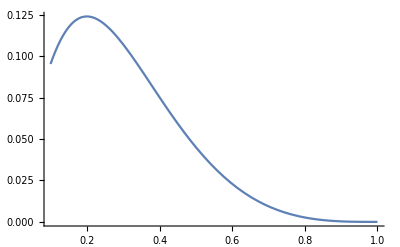

```mathematica
Plot[pHdgu[x,-1],{x,0.1,1},PlotRange->All]
```

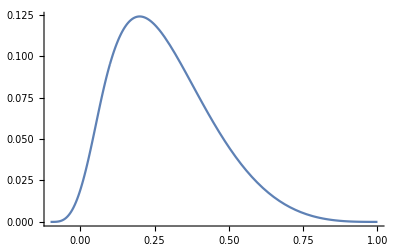

```mathematica
Show[Plot[pHdgu[x,-1],{x,0.1,1},PlotRange->All],Plot[pHeru[x,-1],{x,-0.1,0.1},PlotRange->All]]
```

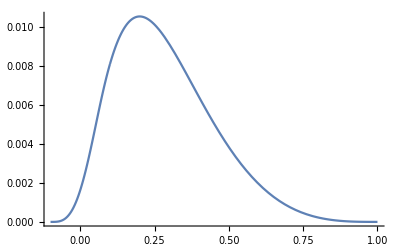

```mathematica
Show[Plot[s1Hdgu[x,-1],{x,0.1,1},PlotRange->All],Plot[s1Heru[x,-1],{x,-0.1,0.1},PlotRange->All]]
```

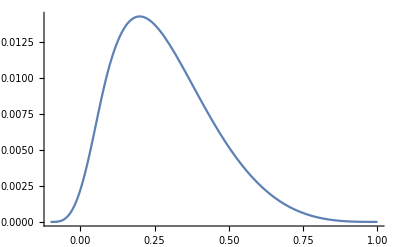

```mathematica
Show[Plot[pHdgu2[x,-1],{x,0.1,1},PlotRange->All],Plot[pHeru2[x,-1],{x,-0.1,0.1},PlotRange->All]]
```

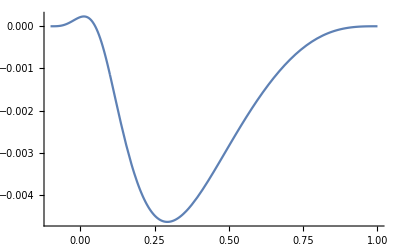

```mathematica
Show[Plot[slHdgu[x,-1],{x,0.1,1},PlotRange->All],Plot[slHeru[x,-1],{x,-0.1,0.1},PlotRange->All]]
```

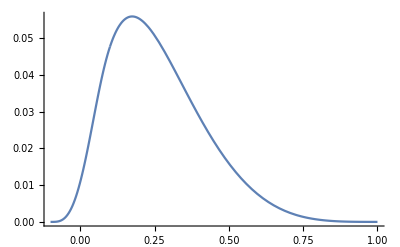

```mathematica
Show[Plot[lHdgu[x,-1],{x,0.1,1},PlotRange->All],Plot[lHeru[x,-1],{x,-0.1,0.1},PlotRange->All]]
```

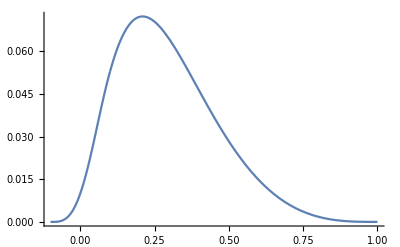

```mathematica
Show[Plot[lHdgs[x,-1],{x,0.1,1},PlotRange->All],Plot[lHers[x,-1],{x,-0.1,0.1},PlotRange->All]]
```

```mathematica
pH=Show[Plot3D[pHdgu[x,t],{x,0.1,1},{t,-1,-0.037},PlotRange->All],Plot3D[pHeru[x,t],{x,-0.1,0.1},{t,-1,-0.037},PlotRange->All],AxesLabel->{"x","t","H^u(x,ξ,t)"},LabelStyle->Directive[Black,Thick,12]]
```

-Graphics3D-

```mathematica
pE=Show[Plot3D[pEdgu[x,t],{x,0.1,1},{t,-1,-0.037},PlotRange->All],Plot3D[pEeru[x,t],{x,-0.1,0.1},{t,-1,-0.037},PlotRange->All],AxesLabel->{"x","t","E^u(x,ξ,t)"},LabelStyle->Directive[Black,Thick,12]]
```

-Graphics3D-

```mathematica
slH=Show[Plot3D[slHdgu[x,t],{x,0.1,1},{t,-1,-0.037},PlotRange->All],Plot3D[slHeru[x,t],{x,-0.1,0.1},{t,-1,-0.037},PlotRange->All],AxesLabel->{"x","t","H^u(x,ξ,t)"},LabelStyle->Directive[Black,Thick,12]]
```

-Graphics3D-

```mathematica
slH=Show[Plot3D[slHdgd[x,t],{x,0.1,1},{t,-1,-0.037},PlotRange->All],Plot3D[slHeru[x,t],{x,-0.1,0.1},{t,-1,-0.037},PlotRange->All],AxesLabel->{"x","t","H^u(x,ξ,t)"},LabelStyle->Directive[Black,Thick,12]]
```